The Hartree-Fock part

the correction parts Ω_n, where n>=2

n = 2

n = 2

{-8}

i = 1

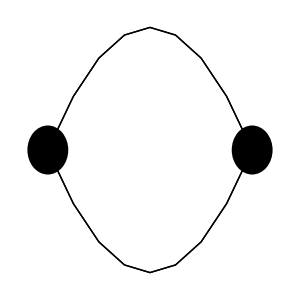

Begin integration

End integration

n = 3

n = 3

{24,6}

i = 1

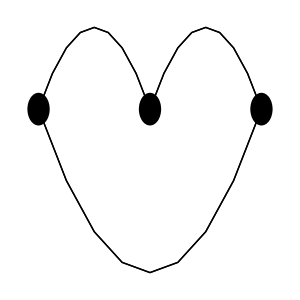

Begin integration

End integration

i = 2

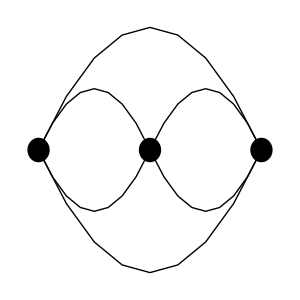

Begin integration

End integration

n = 4

n = 4

{-64,8,-4,-8,4}

i = 1

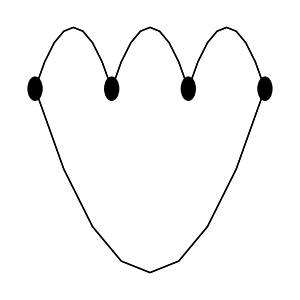

Begin integration

End integration

i = 2

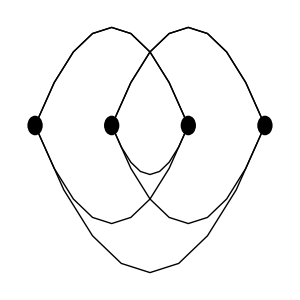

Begin integration

End integration

i = 3

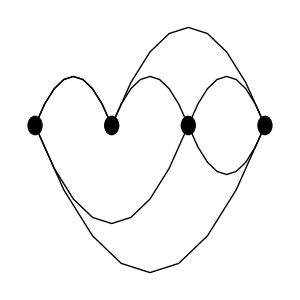

Begin integration

End integration

i = 4

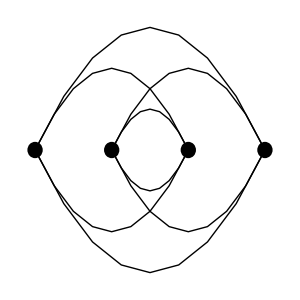

Begin integration

End integration

i = 5

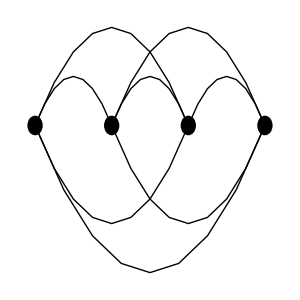

Begin integration

End integration

OmHF

1/16 b^2 U v1 v2+1/4 (-U+2 v1+2 v2)+1/768 b^4 U v1 v2 (-96 t^2+3 U^2-4 v1^2-4 v2^2)+1/8 b (-8 t^2-v1^2-v2^2)+1/384 b^3 (144 t^4+48 t^2 v1^2-3 U^2 v1^2+2 v1^4+48 t^2 v2^2-3 U^2 v2^2+2 v2^4)+(b^6 U v1 v2 (46080 t^4-2880 t^2 U^2+45 U^4+4800 t^2 v1^2-300 U^2 v1^2+96 v1^4+4800 t^2 v2^2-300 U^2 v2^2+80 v1^2 v2^2+96 v2^4))/184320+1/92160 b^5 (-25600 t^6-17280 t^4 v1^2+2160 t^2 U^2 v1^2-45 U^4 v1^2-1920 t^2 v1^4+120 U^2 v1^4-32 v1^6-17280 t^4 v2^2+2160 t^2 U^2 v2^2-45 U^4 v2^2+360 U^2 v1^2 v2^2-1920 t^2 v2^4+120 U^2 v2^4-32 v2^6)-(2 Log[2])/b

Om[2] =

-(b U^2)/32-1/128 b^4 U^3 v1 v2-(b^6 U^3 v1 v2 (-104 t^2+3 U^2-8 v1^2-8 v2^2))/3072+1/384 b^3 U^2 (16 t^2+3 v1^2+3 v2^2)+(b^5 U^2 (-1968 t^4-800 t^2 v1^2+45 U^2 v1^2-40 v1^4-800 t^2 v2^2+45 U^2 v2^2-60 v1^2 v2^2-40 v2^4))/30720

Om[3] =

1/384 b^4 U^3 v1 v2+(b^6 U^3 v1 v2 (-192 t^2+9 U^2-16 v1^2-16 v2^2))/18432-(b^5 U^4 (v1^2+v2^2))/1536

Om[4] =

(b^3 U^4)/3072+(b^6 U^5 v1 v2)/3072-(b^5 U^4 (24 t^2+5 v1^2+5 v2^2))/15360

All orders

1/16 b^2 U v1 v2+1/4 (-U+2 v1+2 v2)+1/32 b (-32 t^2-U^2-4 v1^2-4 v2^2)-1/768 b^4 U v1 v2 (96 t^2+U^2+4 v1^2+4 v2^2)+(b^3 (1152 t^4+128 t^2 U^2+U^4+384 t^2 v1^2+16 v1^4+384 t^2 v2^2+16 v2^4))/3072+(b^6 U v1 v2 (46080 t^4+1440 t^2 U^2+15 U^4+4800 t^2 v1^2+20 U^2 v1^2+96 v1^4+4800 t^2 v2^2+20 U^2 v2^2+80 v1^2 v2^2+96 v2^4))/184320+1/23040 b^5 (-6400 t^6-1476 t^4 U^2-36 t^2 U^4-4320 t^4 v1^2-60 t^2 U^2 v1^2-480 t^2 v1^4-8 v1^6-4320 t^4 v2^2-60 t^2 U^2 v2^2+45 U^2 v1^2 v2^2-480 t^2 v2^4-8 v2^6)-(2 Log[2])/b

```mathematica
(*High-temperature series expansion of the two-dimensional Hubbard model via many-body perturbation theory,where in this article we take the maximum order expansion in terms of the potential U to be seven.*)
nMax=4;(*The maximum many-body order, not editable to more than 7*)
OR=6;(*The maximum order expansion in terms of beta, modifiable to recover more orders*)
(*
v1=h-μ+U/2;
v2=-h-μ+U/2;
*)
Print["The Hartree-Fock part"];
qEn=-t (z1+z1^-1+z2+z2^-1);(*the two dimensional Hubbard energy*)
Af[0]=qEn+v1;
Bf[0]=qEn+v2;
tbi=Table[Coefficient[(U/2) Sum[(EulerE[n,0]/n!)(∑_(j=1)^i (Subscript[bas, j-1])b^j)^n,{n,1,i}],b,i],{i,1,OR}];
Do[
Af[i]=Factor[Coefficient[Coefficient[tbi[[i]]/.Subscript[bas, ih_]->Bf[ih],z1,0],z2,0]];
Bf[i]=Factor[Coefficient[Coefficient[tbi[[i]]/.Subscript[bas, ih_]->Af[ih],z1,0],z2,0]]
,{i,1,OR}];
a00[1]=v1+Sum[b^j Af0[j],{j,1,OR}];
a00[2]=v2+Sum[b^j Bf0[j],{j,1,OR}];
Sf[s_]:=b0[s]+qEn;

sr1=Normal[Series[((-1)/b)Log[1+Exp[-b en]],{b,0,OR}]];
S1I=Coefficient[Coefficient[sr1/.en->b0[1]+qEn,z1,0],z2,0];
S1I=S1I+(S1I/.b0[1]->b0[2]);
srExp=Normal[Series[1/(1+Exp[b sz]),{b,0,OR}]];
ser1=Normal[Series[(Coefficient[Coefficient[srExp/.sz->b0[1]+qEn,z1,0],z2,0]),{b,0,OR}]];
ser2=ser1/.b0[1]->b0[2];
S2I=-U Normal[Series[ser1 ser2,{b,0,OR}]];
HF=Sum[b^i Factor[Coefficient[(S1I+S2I),b,i]],{i,-1,OR}];(*The HTS of Subscript[Ω, HF]*)
Print["the correction parts Ω_n, where n>=2"];
Fn[i_]:=-(1/(1+Exp[b*Subscript[x, i]]));
Fp[i_]:=1/(1+Exp[-b*Subscript[x, i]]);
(*The potential*)
pot[s1_,s2_,s3_,s4_]:=U(1-KroneckerDelta[s1,s2])(KroneckerDelta[s1,s3]KroneckerDelta[s2,s4]-KroneckerDelta[s1,s4]KroneckerDelta[s2,s3]);
En0[i_,s_]:=b0[s]-t(Subscript[X1, i]+Subscript[X1, i]^-1+Subscript[X2, i]+Subscript[X2, i]^-1);
(*Graphical representation of Hugenholtz diagrams (optional)*)
eps=0.10;
ListDisks:=Table[Disk[{i,0},eps],{i,1,n}];
Grph[R_]:=(sg=n;
ListGraph={ListDisks};
Do[If[R[[2 k-1]]==R[[2 k]],AppendTo[ListGraph,Thick];sg--,AppendTo[ListGraph,Thin]];
If[R[[2 k-1]]==k||R[[2 k]]==k,AppendTo[ListGraph,{Black,Thick,Arrowheads[{{Automatic,0.5}}],Circle[{k,0.5},0.45]}]];
If[R[[2 k-1]]≠k,AppendTo[ListGraph,{Arrowheads[{{Automatic,0.5}}],Arrow[BezierCurve[{{k,0},{(k+R[[2 k-1]])/2,R[[2 k-1]]-k},{R[[2 k-1]],0}}]]}]];
If[R[[2 k]]≠k,AppendTo[ListGraph,{Arrowheads[{{Automatic,0.5}}],Arrow[BezierCurve[{{k,0},{(k+R[[2 k]])/2,R[[2 k]]-k},{R[[2 k]],0}}]]}]]
,{k,1,n}];
Return[ListGraph]);
(*Decompresse denominators*)
ToFormD[Den_,Nig_]:=(
Dig=IntegerDigits[Den,2,2n];
Ni=IntegerDigits[Nig,2,2n];
Posi=IntegerDigits[BitXor[Den,Nig],2,2n];
fo=0;
Do[
If[Dig[[j]]==1&&Posi[[j]]==1,
fo+=Subscript[x, 2n+1-j],
If[Dig[[j]]==1&&Ni[[j]]==1,
fo-=Subscript[x, 2n+1-j]]
]
,{j,2n,1,-1}];
Return[fo]
);
(*Decompresse numerators*)
ToFormN[Nom_,SignNom_,SignCoefNom_]:=(
Dig=IntegerDigits[Nom,2,2n];
Posi=IntegerDigits[SignNom,2,2n];
Ni=IntegerDigits[BitXor[SignNom,Nom],2,2n];
fo=1;
Do[
If[Dig[[j]]==1&&Posi[[j]]==1,
fo*=Fn[2n+1-j],
If[Dig[[j]]==1&&Ni[[j]]==1,
fo*=Fp[2n+1-j]]
]
,{j,2n,1,-1}];
fo=fo*SignCoefNom;
Return[fo]
);
(*Integration by coefficients*)
Int[F_,rpl_,Fi_,LiV_]:=(
ResIn=(F/.rpl)/.Fi;
Do[
ResIn=Coefficient[Coefficient[ResIn/.rpl[[iv+1]],LiV[[iv]][[1]],0],LiV[[iv]][[2]],0]
,{iv,1,Length[LiV]}];
Return[ResIn]
);
(*Develeoppement en series*)
parT[ni_,ln_,bg_]:=Flatten[Permutations/@IntegerPartitions[ni,{ln},Range[bg,ni]],1];
SerHT[n_,OR_,rn_,vr_]:=(
tor=0;
Do[
(*Subscript[n, 1]+Subscript[n, 2]+...+Subscript[n, Length[rn]]=NN; where Subscript[n, i] are odds*)
Lini=Flatten[Permutations/@IntegerPartitions[NN,{Length[rn]},Select[Range[1,NN],OddQ]],1];
(*The condition Subscript[n, i]≥Subscript[r, i]*)
LiniEx={};
Do[
sl=True;
Do[
If[Lini[[iz]][[ix]]<rn[[ix]],sl=False;Break[]]
,{ix,1,Length[Lini[[iz]]]}];
If[sl,AppendTo[LiniEx,Lini[[iz]]]]
,{iz,1,Length[Lini]}];
(*Generate the polynomes*)
If[LiniEx≠{},
smT=0;
Do[
pr=1;
Do[
Li1=parT[LiniEx[[iz]][[ix]]-rn[[ix]],rn[[ix]]+1,0];
pr*=-(EulerE[LiniEx[[iz]][[ix]],0]/(2(LiniEx[[iz]][[ix]]!)))Total[Inner[Power,vr[[ix]],#,Times]&/@Li1];
,{ix,1,Length[rn]}];
smT+=pr;
,{iz,1,Length[LiniEx]}];
PolNN[NN,rn]=Expand[smT]
,
PolNN[NN,rn]=0;
]
,{NN,n-1,OR}];
);
GenPolMM[n_,smM_,OR_]:=(
For[NN=n-1,NN≤OR,NN++,
mm=OR-NN;
PolMM[mm]=1/(mm!)D[smM,{b,mm}]/.b->0;
]
);
GenPolNN[n_,OR_]:=(
Ranks=IntegerPartitions[n-1];
Do[
rank=Ranks[[ig]];
Var=FoldPairList[TakeDrop,Table[Subscript[t, i],{i,1,Length[rank]+Total[rank]}],1+rank];
SerHT[n,OR,rank,Var]
,{ig,1,Length[Ranks]}]
);
(*Variables to change, and variables to integrate*)
vrChVrIn[DenNom0_,CTr_,n_]:=(
cc=2^(2n)-1;
Fi={};(*list of variables to change*)
ctr=BitXor[cc,CTr];
Fi0={};
Do[
de=DenNom0[[i]][[1]];
NiD=DenNom0[[i]][[2]];(*Nigatif Denominator*)
PoD=BitXor[de,NiD];(*Positif Denominator*)
bitSt=BitXor[de,BitAnd[ctr,de]];(*The branch i of Spanning Tree*)
PoD=BitXor[PoD,bitSt];(*The only variables without branch*)
NuNiD=IntegerDigits[NiD,2,2n];(*In the form of integers*)
NuPoD=IntegerDigits[PoD,2,2n];(*In the form of integers*)
prNu=1;
prDe=1;
Do[
If[NuNiD[[j]]==1,prNu*=Subscript[X, 2n+1-j]];
If[NuPoD[[j]]==1,prDe*=Subscript[X, 2n+1-j]];
,{j,2n,1,-1}];
cc=BitXor[cc,bitSt];
vrb=BitLength[bitSt];
prt1=(prNu/prDe)/.X->X1;
prt2=(prNu/prDe)/.X->X2;
prt0=(prNu/prDe)/.X->x;
AppendTo[Fi0,Subscript[x, vrb]->prt0];
AppendTo[Fi,Subscript[X1, vrb]->prt1];
AppendTo[Fi,Subscript[X2, vrb]->prt2]
,{i,1,n-1}];
Lid=IntegerDigits[cc,2,2n];
VQ={};(*Variables to integrate over them*)
Do[
If[Lid[[j]]==1,
AppendTo[VQ,{Subscript[X1, 2n+1-j],Subscript[X2, 2n+1-j]}]
]
,{j,2n,1,-1}];
VQ=Sort[VQ];
Return[{Fi,VQ,Fi0}]
);
(*The main code of evaluation*)
Str0 = SetDirectory[NotebookDirectory[]] <> "/GrandPotential";
ALLord=0;
Do[
Hug=ToExpression[Import[Str0 <> ToString[n] <> ".txt"]];
LN = Length[Hug]/5;
LR=Table[Hug[[5*i-4]],{i,1,LN}];
Sym=Table[Hug[[5*i-3]],{i,1,LN}];
DenNom0=Table[Hug[[5*i-2]],{i,1,LN}];
CTr=Table[Hug[[5*i-1]],{i,1,LN}];
DenNom=Table[Hug[[5*i]],{i,1,LN}];
Print["n = ",n];
VQe=Table[Subscript[X, r],{r,1,n+1}];
ls=Flatten[Table[{{Subscript[s, 2i-1],1,2},{Subscript[s, 2i],1,2}},{i,1,n}],1];(*The list of indices of summations over spins*)
Do[orSrI0[or]=0 ,{or,n-1,OR}];
GenPolNN[n,OR];(*Generate the PolyNN*)
Print["n = ",n];
rpL={};
Do[
AppendTo[rpL,Subscript[x, 2i-1]->En0[2i-1,Subscript[s, 2i-1]]];
AppendTo[rpL,Subscript[x, 2i]->En0[2i,Subscript[s, 2i]]];
,{i,1,n}];
SrFI=0;
om[n]=0;
Print[Sym];
Do[
Print["i = ",ii];
Gr=Graphics[Grph[1+LR[[ii]]],ImageSize->{300,300}];
Print[Gr];
POT=Times@@Table[pot[Subscript[s, 2j-1],Subscript[s, 2j],Subscript[s, 2 LR[[ii,2 j-1]]+1],Subscript[s, 2 LR[[ii,2 j]]+2]],{j,1,n}];(*Compute the potential*)
fiVQ=vrChVrIn[DenNom0[[ii]],CTr[[ii]],n];
Fi=fiVQ[[1]];
VQ0=fiVQ[[2]];
Fi0=fiVQ[[3]];
LN2=Length[DenNom[[ii]] ]/4;
Do[orSr0[or]=0,{or,n-1,OR}];
diagC=0;
Do[
sm=DenNom[[ii,4i]] Total[ToFormN[#[[2]],#[[3]],#[[1]]]&/@DenNom[[ii,4i-3]] ];
rn=DenNom[[ii,4i-2]] ;
ord=Ordering[rn,All,Greater];
rn=rn[[ord]];
At={Subscript[x, IntegerLength[#[[1]],2]],ToFormD[#[[1]],#[[2]]]&/@#[[2]]}&/@DenNom[[ii,4i-1]] ;
At=Flatten/@At;
At=At[[ord]];
Var=FoldPairList[TakeDrop,Table[Subscript[t, i],{i,1,Length[rn]+Total[rn]}],1+rn];
trNN=Thread[Flatten[Var]->Flatten[At]];
GenPolMM[n,sm,OR];(*Generate The PolMM*)
Do[
diagC+=b^or Sum[PolNN[NN,rn]*PolMM[or-NN],{NN,n-1,or}]/.trNN
,{or,n-1,OR}
]
,{i,1,LN2}];
Print["Begin integration"];
exPan=Expand[diagC]/.Plus->List;
intList=Total[Int[#,rpL,Fi,VQ0]&/@exPan];
in00=POT intList;
ls00=Prepend[ls,in00];
om[n]+=Factor[Sum@@ls00]/Sym[[ii]];
Print["End integration"];
,{ii,1,LN}]
,{n,2,nMax}];

Do[
om[n]=Sum[b^i Factor[Coefficient[om[n],b,i]],{i,n-1,OR}]
,{n,2,nMax}];
HF=HF/.{b0[1]->a00[1],b0[2]->a00[2]};
HF=Normal[Series[HF,{b,0,OR}]];
HF=HF/.{Af0[ii_]->Af[ii],Bf0[ii_]->Bf[ii]};
HF=Sum[b^i Factor[Coefficient[HF,b,i]],{i,-1,OR}];
Print["OmHF"];
Print[HF];
Do[
om[n]=om[n]/.{b0[1]->a00[1],b0[2]->a00[2]};
om[n]=Normal[Series[om[n],{b,0,OR}]];
om[n]=om[n]/.{Af0[ii_]->Af[ii],Bf0[ii_]->Bf[ii]};
om[n]=Sum[b^i Factor[Coefficient[om[n],b,i]],{i,n-1,OR}];
Print["Om[",n,"] = "];
Print[om[n]]
,{n,2,nMax}];
ALLord+=HF;
ALLord+=Sum[om[n],{n,2,nMax}];
Print["All orders"];
Sum[b^i Factor[Coefficient[ALLord,b,i]],{i,-1,OR}]
```